```mathematica
(*Define single qubit operations, and CZ gates*)
Clear[PiOV2]
H[phi_] := {{0,1/2Exp[-ⅈ phi]},{1/2 Exp[ⅈ phi],0}}
PiOV2[phi_,alpha_] := MatrixExp[- ⅈ H[phi] (π/2+alpha)];PiOV2[0]//MatrixForm
PiOV4[phi_,alpha_] :=  MatrixExp[- ⅈ H[phi]( π/4+alpha/2)];  PiOV4[0]//MatrixForm
CZ := {{1,0,0,0},{0,Exp[-ⅈ ϕ],0,0},{0,0,Exp[-ⅈ ϕ],0},{0,0,0,Exp[-ⅈ (π+2ϕ)]}};CZ//MatrixForm
CZreal = {{1,0,0,0},{0,-0.7171836417978397-0.682774572442743ⅈ,0,0},{0,0,-0.7171836417978397-0.682774572442743ⅈ,0},{0,0,0,-0.028642589618199946-0.9909836454950903ⅈ}}; CZreal//MatrixForm
```

PiOV2[0]

(1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | -1/2 (-1)^(1/8)-1/2 (-1)^(7/8)
-1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | 1/2 (-1)^(1/8)-1/2 (-1)^(7/8))

(1 | 0 | 0 | 0
0 | ⅇ^(-ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(-ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(-ⅈ (π+2 ϕ)))

(1 | 0 | 0 | 0
0 | -0.717184-0.682775 ⅈ | 0 | 0
0 | 0 | -0.717184-0.682775 ⅈ | 0
0 | 0 | 0 | -0.0286426-0.990984 ⅈ)

```mathematica
(*Test bell state preparation in ideal case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
TwoPiOV4 = KroneckerProduct[PiOV4[π-ϕ,alpha],PiOV4[π-ϕ,alpha]];
TwoPiOv2 = KroneckerProduct[PiOV2[0,alpha],PiOV2[0,alpha]];
ϕIdeal  = FullSimplify[TwoPiOV4.CZ.TwoPiOv2.ϕInitial];ϕIdeal//MatrixForm
Refine[Abs[ConjugateTranspose[ϕIdeal].ϕIdeal]^2,Assumptions->{a>0,b>0,ϕ>0}]
```

(1
0
0
0)

(1/8 (3 √2 Cos[alpha/2]+√2 Cos[(3 alpha)/2]-3 √2 Sin[alpha/2]-4 Sin[alpha]+√2 Sin[(3 alpha)/2])
((Cos[alpha/2]+Sin[alpha/2]) Sin[alpha] (ⅈ Cos[ϕ]+Sin[ϕ]))/(2 √2)
((Cos[alpha/2]+Sin[alpha/2]) Sin[alpha] (ⅈ Cos[ϕ]+Sin[ϕ]))/(2 √2)
1/8 ⅇ^(-2 ⅈ ϕ) (3 √2 Cos[alpha/2]+√2 Cos[(3 alpha)/2]-3 √2 Sin[alpha/2]+4 Sin[alpha]+√2 Sin[(3 alpha)/2]))

Abs[1/4 Conjugate[Sin[alpha]] (Cos[alpha/2]+Sin[alpha/2]) Sin[alpha] (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]) (Cos[Conjugate[alpha]/2]+Sin[Conjugate[alpha]/2])+1/64 (3 √2 Cos[alpha/2]+√2 Cos[(3 alpha)/2]-3 √2 Sin[alpha/2]-4 Sin[alpha]+√2 Sin[(3 alpha)/2]) (-4 Conjugate[Sin[alpha]]+3 √2 Cos[Conjugate[alpha]/2]+√2 Cos[(3 Conjugate[alpha])/2]-3 √2 Sin[Conjugate[alpha]/2]+√2 Sin[(3 Conjugate[alpha])/2])+1/64 (3 √2 Cos[alpha/2]+√2 Cos[(3 alpha)/2]-3 √2 Sin[alpha/2]+4 Sin[alpha]+√2 Sin[(3 alpha)/2]) (4 Conjugate[Sin[alpha]]+3 √2 Cos[Conjugate[alpha]/2]+√2 Cos[(3 Conjugate[alpha])/2]-3 √2 Sin[Conjugate[alpha]/2]+√2 Sin[(3 Conjugate[alpha])/2])]^2

### pi/4 pulse phase calibration

(1
0
0
0)

π/10

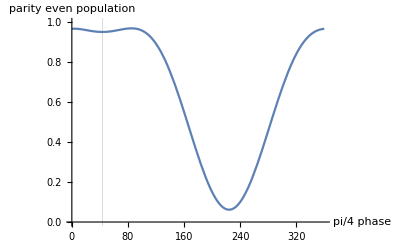

{0.534501+0.0525402 ⅈ,0.100908-0.0277279 ⅈ,0.100908-0.0277279 ⅈ,0.129764+0.810348 ⅈ}

{0.521528-0.00252596 ⅈ,0.0904536-0.0870175 ⅈ,0.0904536-0.0870175 ⅈ,0.0304824+0.824271 ⅈ}

{0.525876-0.0374206 ⅈ,0.0548057-0.100426 ⅈ,0.0548057-0.100426 ⅈ,-0.0390382+0.823535 ⅈ}

{0.539747-0.159214 ⅈ,-0.0749339-0.0524241 ⅈ,-0.0749339-0.0524241 ⅈ,-0.193464+0.78296 ⅈ}

```mathematica
(*Realistic case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
alpha = π/10
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ,alpha],PiOV4[θ,alpha]];
TwoPiOv2 = KroneckerProduct[PiOV2[0,alpha],PiOV2[0,alpha]];
ϕexp[θ_]  := FullSimplify[TwoPiOv4[θ].CZreal.TwoPiOv2.ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[1]]]^2 +Abs[ϕexp[θ*π/180][[4]]]^2 ,{θ,0,360},AxesLabel-> { "pi/4 phase","parity even population"},GridLines->{{43.59203140981553},{}},PlotRange->{0,1}]
ϕexp[20*π/180]
ϕexp[43.5*π/180]
ϕexp[60*π/180]
ϕexp[93.5*π/180]
```

#### one of even component

(1
0
0
0)

π/10

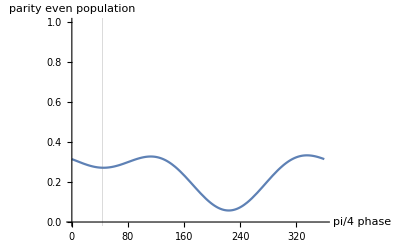

{0.534501+0.0525402 ⅈ,0.100908-0.0277279 ⅈ,0.100908-0.0277279 ⅈ,0.129764+0.810348 ⅈ}

{0.521528-0.00252596 ⅈ,0.0904536-0.0870175 ⅈ,0.0904536-0.0870175 ⅈ,0.0304824+0.824271 ⅈ}

{0.525876-0.0374206 ⅈ,0.0548057-0.100426 ⅈ,0.0548057-0.100426 ⅈ,-0.0390382+0.823535 ⅈ}

{0.539747-0.159214 ⅈ,-0.0749339-0.0524241 ⅈ,-0.0749339-0.0524241 ⅈ,-0.193464+0.78296 ⅈ}

```mathematica
(*Realistic case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
alpha = π/10
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ,alpha],PiOV4[θ,alpha]];
TwoPiOv2 = KroneckerProduct[PiOV2[0,alpha],PiOV2[0,alpha]];
ϕexp[θ_]  := FullSimplify[TwoPiOv4[θ].CZreal.TwoPiOv2.ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[1]]]^2 ,{θ,0,360},AxesLabel-> { "pi/4 phase","parity even population"},GridLines->{{43.59203140981553},{}},PlotRange->{0,1}]
ϕexp[20*π/180]
ϕexp[43.5*π/180]
ϕexp[60*π/180]
ϕexp[93.5*π/180]
```

(1
0
0
0)

π/10

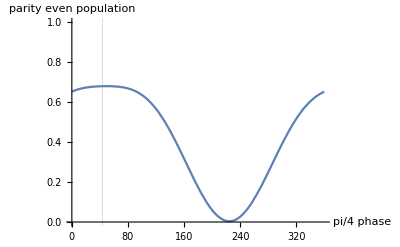

{0.534501+0.0525402 ⅈ,0.100908-0.0277279 ⅈ,0.100908-0.0277279 ⅈ,0.129764+0.810348 ⅈ}

{0.521528-0.00252596 ⅈ,0.0904536-0.0870175 ⅈ,0.0904536-0.0870175 ⅈ,0.0304824+0.824271 ⅈ}

{0.525876-0.0374206 ⅈ,0.0548057-0.100426 ⅈ,0.0548057-0.100426 ⅈ,-0.0390382+0.823535 ⅈ}

{0.539747-0.159214 ⅈ,-0.0749339-0.0524241 ⅈ,-0.0749339-0.0524241 ⅈ,-0.193464+0.78296 ⅈ}

```mathematica
(*Realistic case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
alpha = π/10
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ,alpha],PiOV4[θ,alpha]];
TwoPiOv2 = KroneckerProduct[PiOV2[0,alpha],PiOV2[0,alpha]];
ϕexp[θ_]  := FullSimplify[TwoPiOv4[θ].CZreal.TwoPiOv2.ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[4]]]^2 ,{θ,0,360},AxesLabel-> { "pi/4 phase","parity even population"},GridLines->{{43.59203140981553},{}},PlotRange->{0,1}]
ϕexp[20*π/180]
ϕexp[43.5*π/180]
ϕexp[60*π/180]
ϕexp[93.5*π/180]
```

(1
0
0
0)

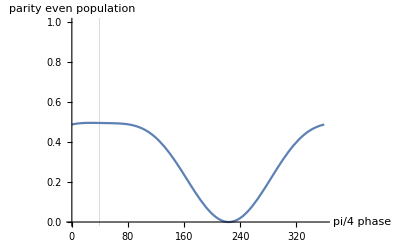

```mathematica
(*Realistic case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ],PiOV4[θ]];
TwoPiOv2 = KroneckerProduct[PiOV2[0],PiOV2[0]];
ϕexp[θ_]  := FullSimplify[TwoPiOv4[θ].CZreal.TwoPiOv2.ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[1]]]^2  ,{θ,0,360},AxesLabel-> { "pi/4 phase","parity even population"},GridLines->{{39.6},{}},PlotRange->{0,1}]
```

(1
0
0
0)

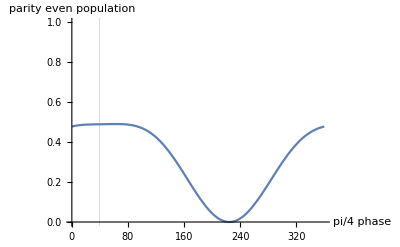

```mathematica
(*Realistic case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ],PiOV4[θ]];
TwoPiOv2 = KroneckerProduct[PiOV2[0],PiOV2[0]];
ϕexp[θ_]  := FullSimplify[TwoPiOv4[θ].CZreal.TwoPiOv2.ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[4]]]^2  ,{θ,0,360},AxesLabel-> { "pi/4 phase","parity even population"},GridLines->{{39.6},{}},PlotRange->{0,1}]
```

### Parity oscillation

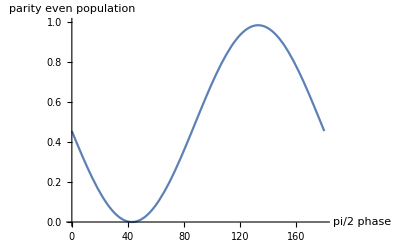

```mathematica
TwoPiOV2[ϕ_] := KroneckerProduct[PiOV2[ϕ],PiOV2[ϕ]];
ϕparity[ϕ_]  := FullSimplify[TwoPiOV2[ϕ].ϕexp[39.6*π/180]]
Plot[Abs[ϕparity[ϕ*π/180][[1]]]^2 +Abs[ϕparity[ϕ*π/180][[4]]]^2 ,{ϕ,0,180},AxesLabel-> { "pi/2 phase","parity even population"},PlotRange->{0,1}]
```

### Single atom behavior

```mathematica
(*Define single qubit operations, and CZ gates*)
Clear[PiOV2]
H[phi_] := {{0,1/2Exp[-ⅈ phi]},{1/2 Exp[ⅈ phi],0}}
PiOV2[phi_] := MatrixExp[- ⅈ H[phi] π/2];PiOV2[0]//MatrixForm
PiOV4[phi_] :=  MatrixExp[- ⅈ H[phi] π/4];  PiOV4[0]//MatrixForm
CZ := {{1,0,0,0},{0,Exp[-ⅈ ϕ],0,0},{0,0,Exp[-ⅈ ϕ],0},{0,0,0,Exp[-ⅈ (π+2ϕ)]}};CZ//MatrixForm
CZreal = {{1,0,0,0},{0,-0.7171836417978397-0.682774572442743ⅈ,0,0},{0,0,-0.7171836417978397-0.682774572442743ⅈ,0},{0,0,0,-0.028642589618199946-0.9909836454950903ⅈ}}; CZreal//MatrixForm
```

(1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2))

(1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | -1/2 (-1)^(1/8)-1/2 (-1)^(7/8)
-1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | 1/2 (-1)^(1/8)-1/2 (-1)^(7/8))

(1 | 0 | 0 | 0
0 | ⅇ^(-ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(-ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(-ⅈ (π+2 ϕ)))

(1 | 0 | 0 | 0
0 | -0.717184-0.682775 ⅈ | 0 | 0
0 | 0 | -0.717184-0.682775 ⅈ | 0
0 | 0 | 0 | -0.0286426-0.990984 ⅈ)

```mathematica
(*Test bell state preparation in ideal case*)
ϕInitial = {1,0};ϕInitial//MatrixForm
TwoPiOV4 = KroneckerProduct[PiOV4[π-ϕ],PiOV4[π-ϕ]];
TwoPiOv2 = KroneckerProduct[PiOV2[0],PiOV2[0]];
ϕIdeal  = FullSimplify[PiOV4[π-ϕ].CZ[[1;;2,1;;2]].PiOV2[0].ϕInitial];ϕIdeal//MatrixForm
CZ[[1;;2,1;;2]]//MatrixForm
Refine[Abs[ConjugateTranspose[ϕIdeal].ϕIdeal]^2,Assumptions->{a>0,b>0,ϕ>0}]
```

(1
0)

((√(2+√2))/2
ⅇ^(-ⅈ ϕ) Root-0.383 ⅈRoot[1+8 #1^2+8 #1^4&,3]0.)

(1 | 0
0 | ⅇ^(-ⅈ ϕ))

(1/4 (2+√2)+Root-0.383 ⅈRoot[1+8 #1^2+8 #1^4&,3]0. Root0.383 ⅈRoot[1+8 #1^2+8 #1^4&,4]0.)^2

### pi/4 pulse phase calibration

(1
0)

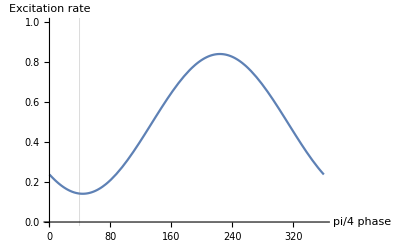

43.592

{0.76247+0.244695 ⅈ,-0.548989+0.218272 ⅈ}

```mathematica
(*Realistic case*)
ϕInitial = {1,0};ϕInitial//MatrixForm
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ],PiOV4[θ]];
TwoPiOv2 = KroneckerProduct[PiOV2[0],PiOV2[0]];
ϕexp[θ_]  := FullSimplify[PiOV4[θ].CZreal[[1;;2,1;;2]].PiOV2[0].ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[2]]]^2  ,{θ,0,360},AxesLabel-> { "pi/4 phase","Excitation rate"},GridLines->{{39.6},{}},PlotRange->{0,1}]
OPtimaldeg = ArgMin[Abs[ϕexp[θ*π/180][[2]]]^2,θ]
ϕexp[OPtimaldeg]
```

#### one of even component

```mathematica
(*Realistic case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ],PiOV4[θ]];
TwoPiOv2 = KroneckerProduct[PiOV2[0],PiOV2[0]];
ϕexp[θ_]  := FullSimplify[TwoPiOv4[θ].CZreal.TwoPiOv2.ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[1]]]^2  ,{θ,0,360},AxesLabel-> { "pi/4 phase","parity even population"},GridLines->{{39.6},{}},PlotRange->{0,1}]
```

(1
0
0
0)

-Graphics-

```mathematica
(*Realistic case*)
ϕInitial = {1,0,0,0};ϕInitial//MatrixForm
TwoPiOv4[θ_] := KroneckerProduct[PiOV4[θ],PiOV4[θ]];
TwoPiOv2 = KroneckerProduct[PiOV2[0],PiOV2[0]];
ϕexp[θ_]  := FullSimplify[TwoPiOv4[θ].CZreal.TwoPiOv2.ϕInitial]
Plot[Abs[ϕexp[θ*π/180][[4]]]^2  ,{θ,0,360},AxesLabel-> { "pi/4 phase","parity even population"},GridLines->{{39.6},{}},PlotRange->{0,1}]
```

(1
0
0
0)

-Graphics-

### Parity oscillation

```mathematica
TwoPiOV2[ϕ_] := KroneckerProduct[PiOV2[ϕ],PiOV2[ϕ]];
ϕparity[ϕ_]  := FullSimplify[TwoPiOV2[ϕ].ϕexp[39.6*π/180]]
Plot[Abs[ϕparity[ϕ*π/180][[1]]]^2 +Abs[ϕparity[ϕ*π/180][[4]]]^2 ,{ϕ,0,180},AxesLabel-> { "pi/2 phase","parity even population"},PlotRange->{0,1}]
```

-Graphics-